```mathematica
SetDirectory["~/Documents/pdr/PDR_upgrade/input_files/"]
```

/home/silke/Documents/pdr/PDR_upgrade/input_files

```mathematica
Al=Import["AlAV.dat","Table"];
Al=Delete[Al,{{1},{2},{3}}];
```

```mathematica
Al=Al[[All,{1,2}]];
```

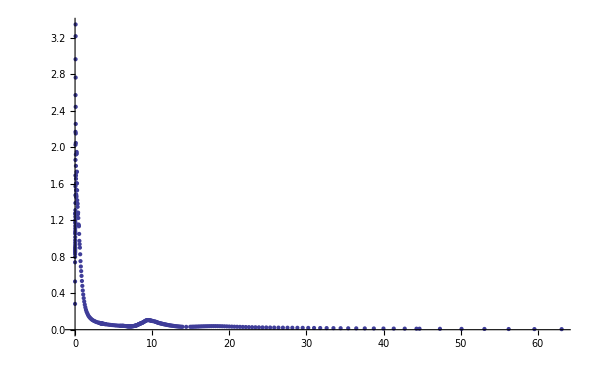

```mathematica
ListPlot[Al]
```

```mathematica
Alint=Interpolation[Al]
```

InterpolatingFunction[{{0.001,3100.}},<>]

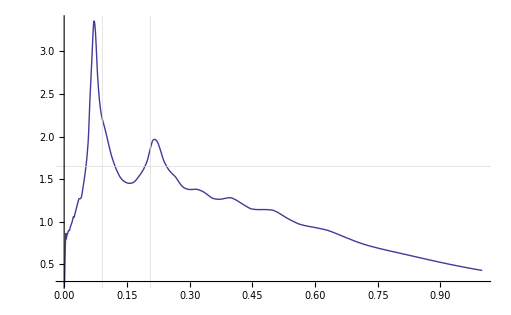

```mathematica
Plot[Alint[l],{l,0.001,1},GridLines->{{0.0912, 0.2067},{1.649}}]
```

```mathematica
Integrate[Alint[l],{l,0.0912,0.2067}]/(0.2067-0.0912)
```

1.64947